# Chapter 5-CIRCULAR MOTION—GRAVITATION

Peter Burbery

Abstract

## Section

XXXX:

## 5-1 to 5-3 Uniform Circular Motion

### 1. (I) A child sitting 1.20 m from the center of a merry-go-round moves with a speed of 1.10 m·s^-1. Calculate {a} the centripetal acceleration of the child and {b} the net horizontal force exerted on the child (mass=22.5 kg).

View possible formulas for centripetal acceleration:

```mathematica
AssociationMap[FormulaData][FormulaLookup["CentripetalAcceleration"]]
```

<|{CentripetalAcceleration,RotationSpeed}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,AngularVelocity}→a Acceleration==r Radius (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,Diameter}→a Acceleration==1/2 d Diameter (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→a Acceleration==(ω AngularVelocity)^2 d_o Distance,{CentripetalAcceleration,OrbitSpeed}→a Acceleration==(v Speed)^2/(d_o Distance),{CentripetalAcceleration,OrbitSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,OrbitSpeed,Radius}→a Acceleration==(v Speed)^2/(r Radius),{CentripetalAcceleration,RotationRate}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 r Radius,{CentripetalAcceleration,RotationRate,Diameter}→a Acceleration==(2 π^2 /rev^2) d Diameter (n RevolutionRate)^2,{CentripetalAcceleration,RotationRate,OrbitDistance}→a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 d_o Distance,{CentripetalAcceleration,RotationSpeed,Diameter}→a Acceleration==(2 (v Speed)^2)/(d Diameter),{CentripetalAcceleration,RotationSpeed,OrbitDistance}→a Acceleration==(v Speed)^2/(d_o Distance)|>

I will use the formula CentripetalAcceleration with RotationSpeed.

Get data for the formula:

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"}]
```

a Acceleration==(v Speed)^2/(r Radius)

The table has lots of helpful information:

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
a | centripetal acceleration | Acceleration | {{LengthUnit,1},{TimeUnit,-2}}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

#### Formula Classes

I wonder what classes this formula is in.

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"Classes"]
```

{Physics,{Physics,Mechanics}}

I wonder what other formulas are in the classes:

Make a word cloud for each class:

```mathematica
PersistResourceFunction["FromCamelCase"]
```

Success[…]

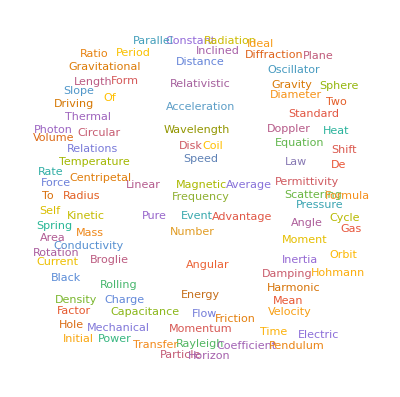

```mathematica
WordCloud[Flatten[TextWords[FromCamelCase[#]]&/@Flatten[FormulaLookup["Physics"]]]]
```

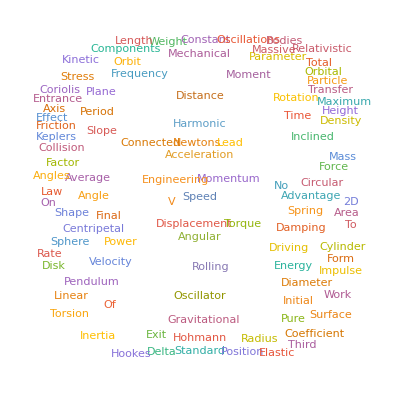

```mathematica
WordCloud[Flatten[TextWords[FromCamelCase[#]]&/@Flatten[FormulaLookup[{"Physics","Mechanics"}]]]]
```

#### using the formula for part a

The child is sitting 1.20m from the merry-go-round so the radius is 1.20m. The speed or velocity is 1.10 m·s^-1.

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]
```

{a Acceleration,r Radius,v Speed}

I just need the rest of the variables, not a:

```mathematica
Rest[FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]]
```

{r Radius,v Speed}

```mathematica
substitutionRules=AssociationThread[Rest[FormulaData[{"CentripetalAcceleration", "RotationSpeed"},"QuantityVariables"]]->{Quantity[1.2, "Meters"],Quantity[1.1, ("Meters")/("Seconds")]}]
```

<|r Radius→1.2 m,v Speed→1.1 m/s|>

```mathematica
FormulaData[{"CentripetalAcceleration","RotationSpeed"}]/.substitutionRules
```

a Acceleration==1.00833 m/s^2

I'm curious what a rationalized form of this is.

```mathematica
Rationalize[FormulaData[{"CentripetalAcceleration","RotationSpeed"}]/.substitutionRules]
```

a Acceleration==121/120 m/s^2

#### part b

```mathematica
substitutionRules//=AppendTo[First[]]
```

```mathematica
FormulaLookup["CentripetalForce"]
```

{{CentripetalForce,RotationSpeed},{CentripetalForce,AngularVelocity}}

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
Rest[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]
```

{m Mass,r Radius,v Speed}

```mathematica
substitutionRules=AssociationThread[Rest[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]->Prepend[(Quantity[22.5, "Kilograms"])][Values[substitutionRules]]]
```

<|m Mass→22.5 kg,r Radius→1.2 m,v Speed→1.1 m/s|>

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]/.substitutionRules
```

F Force==22.6875 kg m/s^2

```mathematica
Rationalize[FormulaData[{"CentripetalForce","RotationSpeed"}]/.substitutionRules]
```

F Force==363/16 kg m/s^2

### 3. (I) A horizontal force of 310 N is exerted on a 2.0-kg ball as it rotates (at arm's length) uniformly in a horizontal circle of radius 900 mm. Calculate the speed of the ball.

#### Initial work

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
F | centripetal force | Force | {{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}
m | mass | Mass | {MassUnit,1}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed"]
```

{{v Speed→-(√(F Force) √(r Radius))/(√(m Mass))},{v Speed→(√(F Force) √(r Radius))/(√(m Mass))}}

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",]
```

{{v Speed→ConditionalExpression[√((F Force r Radius)/(m Mass)), F Force>0&&m Mass>0&&r Radius>0]}}

```mathematica
#>0&/@FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]
```

{F Force>0,m Mass>0,r Radius>0,v Speed>0}

```mathematica
Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]
```

F Force>0&&m Mass>0&&r Radius>0

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]
```

{{v Speed→√((F Force r Radius)/(m Mass))}}

```mathematica
substitutionRules=AssociationThread[{"F" "Force","r" "Radius","m" "Mass"}->{Quantity[310, "Newtons"],Quantity[900, "Millimeters"],Quantity[2., "Kilograms"]}]
```

<|F Force→310 N,r Radius→900 mm,m Mass→2. kg|>

```mathematica
Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules
```

{{v Speed→373.497 √mm √N/√kg}}

```mathematica
UnitSimplify[Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules]
```

{{v Speed→11.811 m/s}}

```mathematica
Rationalize[UnitSimplify[Solve[FormulaData[{"CentripetalForce","RotationSpeed"},"Formula"],"v" "Speed",,Assumptions->Apply[And][#>0&/@Most[FormulaData[{"CentripetalForce","RotationSpeed"},"QuantityVariables"]]]]/.substitutionRules]]
```

{{v Speed→11.811 m/s}}

#### Notes and comments

I reworded this problem slightly to use millimeters in place of millimeters to be in accordance with NIST SP 811 Chapter 7 Section 9 Choosing SI Prefixes. The original wording was

A horizontal force of 310 N is exerted on a 2.0-kg ball as it rotates (at arm’s length) uniformly in a horizontal circle of radius 0.90 m. Calculate the speed of the ball.

There is a discrepancy here in that when I say 900 mm I have three significant figures but 0.90 m has only two significant figures. I changed this to 900 mm even though there was a discrepancy because it realistic to measure something to nearest millimeter instead of to the nearest centimeter, which is the practice in metric architecture and CAD where all dimensions are in millimeters. If this discrepancy is to be avoided, the problem should solved with something like 9.0E2 mm. If 3 significant figures were known, as is the case for 900 mm, I would write 9.00E2 mm.

There is one other thing with this that I think should be changed which instead of saying a 2.0-kg ball, something like a ball of mass 2.0 kg is better. This is explained in NIST SP 811 Chapter 7 Section 2 Space between numerical value and unit symbol.

In summary, I would revise the question to something like this:

A horizontal force of 310 N is exerted on a ball of mass 2.0 kg as it rotates (at arm’s length) uniformly in a horizontal circle of radius 900 mm. Calculate the speed of the ball.

### 5. (II) A 0.55-kg ball, attached to the end of a horizontal cord, is revolved in a circle of radius